```mathematica
Some definitions and functions we will need later on:
```

Syntax::sntxi: Incomplete expression; more input is needed .

```mathematica
λ1={{0,1,0},{1,0,0},{0,0,0}};
λ2={{0,-ⅈ,0},{ⅈ,0,0},{0,0,0}};
λ3={{1,0,0},{0,-1,0},{0,0,0}};
λ4={{0,0,1},{0,0,0},{1,0,0}};
λ5={{0,0,-ⅈ},{0,0,0},{ⅈ,0,0}};
λ6={{0,0,0},{0,0,1},{0,1,0}};
λ7={{0,0,0},{0,0,-ⅈ},{0,ⅈ,0}};
λ8={{1,0,0},{0,1,0},{0,0,-2}}/Sqrt[3];
F1= λ1/2;
F2= λ2/2;
F3= λ3/2;
F4= λ4/2;
F5= λ5/2;
F6= λ6/2;
F7= λ7/2;
F8= λ8/2;
Y=2F8 / Sqrt[3];
Iplus=F1+ ⅈ F2;
Iminus=F1- ⅈ F2;
I0=F3;
Vplus=F4+ ⅈ F5;
Vminus=F4- ⅈ F5;
V0= (Vplus.Vminus-Vminus.Vplus)/2;
Uplus=F6+ ⅈ F7;
Uminus=F6- ⅈ F7;
U0= (Uplus.Uminus-Uminus.Uplus)/2;
GetHamiltonian[list_]:=(s=0;Do[w= D[Part[list,iterator2,1],z]*IdentityMatrix[3];Do[w=w.Evaluate[MatrixExp[ Part[list,iterator1,1]*Part[list,iterator1,2]]],{iterator1,iterator2-1}];
w= w.Part[list,iterator2,2];Do[w=w.Evaluate[MatrixExp[-Part[list,iterator2-iterator1,1]*Part[list,iterator2-iterator1,2]]],{iterator1,iterator2-1}];s=s+w,{iterator2,Length[list]}];Return[s]);
GetPropagator[list_]:=(
w=IdentityMatrix[3];
Do[w=w.MatrixExp[ Part[list,iterator,1]*Part[list,iterator,2]],{iterator,Length[list]}];
Return[w]
);
```

### The module for the numerical solution

```mathematica
FN[Asub_, Bsub_]:=Module[{list, listOfFunctions, listOfDerivatives, res, eqs, sol, solNumerical, eqs1,ode},
list =List[{ⅈ ιp[z],Iplus},{ⅈ μp[z],Uplus},{ⅈ  νp[z],Vplus},
{ⅈ  ι0[z],I0},{ⅈ  y0[z],Y},{ⅈ  ey[z],IdentityMatrix[3]},
{ⅈ  νm[z],Vminus},{ⅈ  μm[z],Uminus},{ⅈ  ιm[z],Iminus}];
listOfFunctions = {ιp[z], μp[z],  νp[z],
ι0[z],y0[z],ey[z],
νm[z], μm[z], ιm[z]};
listOfDerivatives=D[#,z]&/@listOfFunctions;
(res=FullSimplify[GetHamiltonian[list]]);
H=({{0, g[z], g[z]}, {g[z], 0, g[z]}, {g[z], g[z], 0}});
eqs=Thread[(Flatten[res]==Flatten[ ⅈ H])];
sol=FullSimplify[Solve[eqs,listOfDerivatives]];
eqs1=Thread[listOfDerivatives==((listOfDerivatives/.sol)[[1]])];
ode = Join[eqs1,{ιp[0]==0,ι0[0]==0,ιm[0]==0,νp[0]==0,y0[0]==0,νm[0]==0,μp[0]==0,μm[0]==0, ey[0]==0}];
solNumerical = NDSolve[ode/.{g[z]->Asub+Bsub z},listOfFunctions,{z,0,15}];
solNumerical];
```

### The module for the analytical solution

```mathematica
FA[Asub_, Bsub_]:=Module[{fun, eq1, sol1, eq2, sol2, sol3, sol4, sol5, extraTerm},
fun:={g[z]->A+B z};
eq1:=D[ι[z],z]==g[z]-ⅈ g[z] ι[z]+2g[z] ι[z]ι[z];
sol1=DSolve[{eq1,ι[0]==0}/.fun,ι[z],z][[1]];
eq2:=D[μ[z],z]==(g[z]+ⅈ g[z] ι[z] )+(g[z]+ⅈ g[z] ι[z] )μ[z]μ[z] ;
sol2 =DSolve[{eq1,eq2,ι[0]==0,μ[0]==0}/.fun,{ι[z],μ[z]},z][[1]];
sol3 = FullSimplify[sol2];
sol4 = FullSimplify[D[sol3, z]];
extraTerm = ((3 A z+3/2B z z)+ⅈ Log[Exp[ⅈ (3 A z+3/2B z z)]]);
sol5 = {y0[z] -> -ⅈ/2 Log[ι'[z]μ'[z](1+ⅈ μ[z])/(g[z]g[z](1+ⅈ ι[z]))]+extraTerm/2, 
ι0[z]-> -ⅈ Log[ι'[z]/μ'[z](1+ⅈ μ[z])(1+ⅈ ι[z])]-extraTerm}; Join[sol2,sol5/.fun/.sol4/.sol2,{ et ->extraTerm}]/.{A->Asub, B->Bsub}];
```

### Now we can compare numerical and the analytical solutions and make sure the results are the same (g[z]=1+0.5z)

```mathematica
solN=FN[1, 0.5];
solA =FA[1, 0.5];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

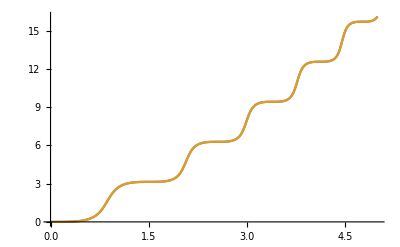

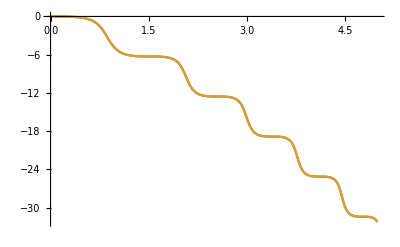

```mathematica
Plot[{Re[y0[z]]/.solN,Re[y0[z]]/.solA}, {z,0,5}]
Plot[{Re[ι0[z]]/.solN,Re[ι0[z]]/.solA}, {z,0,5}]
```

### Now we can plot two random trajectories

```mathematica
list=List[{ⅈ ι[z],Iplus},{ⅈ μ[z],Uplus},{ⅈ  ι[z],Vplus},
{ⅈ  ι0[z],I0},{ⅈ  y0[z],Y},{ⅈ  0,IdentityMatrix[3]},
{ⅈ  ι[z],Vminus},{ⅈ  μ[z],Uminus},{ⅈ  ι[z],Iminus}];
U=Simplify[GetPropagator[list]/.solA];
f1=U.Normalize[{1, 1ⅈ, .4}];
f2=U.Normalize[{.1, 1ⅈ, -.4+.2i}];
surface=SphericalPlot3D[1,{θ,0,Pi/2},{ϕ,0, Pi/2}, PlotStyle->Directive[LightBlue,Opacity[1]], Mesh->None, BoundaryStyle->Gray,ViewPoint->{5,2.5,1},BoxRatios->{1,1,1}, TicksStyle->Directive[FontOpacity->0,FontSize->0], ImageSize->300];
trajectory1= ParametricPlot3D[Abs[f1],{z,0,40},PlotStyle->{LightRed}];
trajectory2= ParametricPlot3D[Abs[f2],{z,0,40},PlotStyle->{LightBlue}];
Show[surface, trajectory1, trajectory2,AxesOrigin->{0,0,0},PlotRange->{{0,1},{0,1},{0,1}}]
```

-Graphics3D-

```mathematica
sol = FA[A,B];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

```mathematica
FullSimplify[(y0[z]-et/2)/.sol]//TeXForm
```

-\frac{1}{2} i \log \left(\frac{27 e^{\frac{3}{2} i z (2 A+B z)}}{\left(2+e^{\frac{3}{2} i z (2 A+B z)}\right)^3}\right)

```mathematica
FullSimplify[(ι0[z]+et)/.sol]//TraditionalForm
```

-ⅈ log((3 ⅇ^(3/2 ⅈ z (2 A+B z)) (2+ⅇ^(3/2 ⅈ z (2 A+B z)))^2 (1+tanh(1/2 log(1/3 (1+2 ⅇ^(3/2 ⅈ z (2 A+B z)))))))/((1+2 ⅇ^(3/2 ⅈ z (2 A+B z)))^3))

```mathematica
FullSimplify[(et)/.sol]//TeXForm
```

\frac{3}{2} z (2 A+B z)+i \log \left(e^{\frac{3}{2} i z (2 A+B z)}\right)